```mathematica
(*Gabriel Soares Rocha, Lorenzo Gavassino, Mayank Singh, and Jean-Francois Paquet*)
(*when using this code or alterations thereof, please cite arXiv:2405.10401[hep-ph]*)
```

## Solving ideal cylindrical boost-invariant hydrodynamics (1+1D)

### Arbitrary initial conditions, arbitrary equation of state (speed of sound)

Equations to be solved for u^τ=cosh κ(τ,r); u^r=sinh κ(τ,r); and ln T(τ, r)

```mathematica
hbarc=.1973(*GeV^-1 fm^-1*);
(*Grid range parameters*)
rmax=50.;taumax=50.;
(*Equation of motion solver -- inputs: τ_0 (in fm), initial condition profiles T(τ_0, r)(in MeV) and κ(τ_0, r) and cs2(T)*)
cylindricalBoostInvariantInviscidGeneral[tau0infm_,initCondT0Fct_,initCondkappaFct_,cs2Fct_]:=(

sols=NDSolve[{D[LogT[tau,r],tau]+Tanh[kappa[tau,r]]D[LogT[tau,r],r]==-(cs2Fct[Exp[LogT[tau,r]]]) (1/tau+Tanh[kappa[tau,r]]/r+Tanh[kappa[tau,r]] D[kappa[tau,r],tau]+D[kappa[tau,r],r]),D[kappa[tau,r],tau]+Tanh[kappa[tau,r]]D[kappa[tau,r],r]==-D[LogT[tau,r],r]/Cosh[kappa[tau,r]]^2+Tanh[kappa[tau,r]] cs2Fct[Exp[LogT[tau,r]]] (1/tau+Tanh[kappa[tau,r]]/r+Tanh[kappa[tau,r]] D[kappa[tau,r],tau]+D[kappa[tau,r],r]),LogT[tau0infm,r]==Log[initCondT0Fct[r]/hbarc],kappa[tau0infm,r]==initCondkappaFct[r]},{LogT,kappa},{tau,tau0infm,taumax},{r,10^-4,rmax},AccuracyGoal->8,PrecisionGoal->Infinity(*,InterpolationOrder->6*)];
tmplogTres=LogT/.sols[[1]];
tmpkappares=kappa/.sols[[1]];

Return[{tmplogTres,tmpkappares}];
)
```

## Cooper - Frye hypersurface and observables

```mathematica
(* Hypersurface finder -- Returns a hypersurface discretized uniformly in r or in tau as a list with entries {τ_i, r_i, dτ_i, dr_i, κ(τ_i,r_i),T(τ_i,r_i)} *)

findHyperSurface[logTProfile_,kappaProfile_,TFO_,NDisc_]:=(

(* We assume that the hypersurface is bound within the available range of the hydro solution --- we'll check later that it's the case *)
{{tauMinInterp,tauMaxInterp},{rMinInterp,rMaxInterp}}=ResourceFunction["InterpolatingFunctionDomain"][logTProfile];

(* Find the radius where the temperature profile is equal to TFO at tau=tau0 *)
r0=r/.FindRoot[Exp[logTProfile[tauMinInterp,r]]hbarc==TFO,{r,(rMinInterp+rMaxInterp)/2.,rMinInterp,rMaxInterp}];

(* Find time derivative and radial derivative of log-temperature profile *)
dlogTdtauPre=D[logTProfile[tauEval,rEval],tauEval];
dlogTdtau[tau_?NumericQ,r_?NumericQ]:=dlogTdtauPre/.{tauEval->tau,rEval->r};
dlogTdrPre=D[logTProfile[tauEval,rEval],rEval];
dlogTdr[tau_?NumericQ,r_?NumericQ]:=dlogTdrPre/.{tauEval->tau,rEval->r};

(* Estimate the range where an accurate parametric solution of the hypersurface is necessary *)
rPosApprox=r0;
tauPosApprox=tauMinInterp;
dchitmp=0.1;
chitmp=0;
While[rPosApprox>0,
rPosApprox+=dchitmp*(dlogTdtau[tauPosApprox,rPosApprox]);
tauPosApprox+=dchitmp*(-dlogTdr[tauPosApprox,rPosApprox]);
chitmp+=dchitmp;
];
(*Print["chirange=",chitmp];
Print["tauPosApprox=",tauPosApprox,", rPosApprox=",rPosApprox];*) 
chimaxGuess=1.5*chitmp;
Clear[rPosApprox,tauPosApprox,dchitmp,chitmp];

(* The hypersurface can be found by finding tau(chi),r(chi) such that dlnT(tau(chi),r(chi))/dchi=0, which means dlnT(tau(chi),r(chi))/dtau dtau/dchi+dlnT(tau(chi),r(chi))/dr dr/dchi *)
{tauFOinterp,rFOinterp}={tauFO,rFO}/.NDSolve[{D[tauFO[chi],chi]==-dlogTdr[tauFO[chi],rFO[chi]],D[rFO[chi],chi]==dlogTdtau[tauFO[chi],rFO[chi]],tauFO[0]==tauMinInterp,rFO[0]==r0},{tauFO,rFO},{chi,0,chimaxGuess}][[1]];

(* Range of chi *)
{{chiMin,chiMax}}=ResourceFunction["InterpolatingFunctionDomain"][tauFOinterp];

chiMaxFO=chi/.FindRoot[rFOinterp[chi]==0.0,{chi,chiMax/2.,chiMin,.99*chiMax}];

(* If everything is going well, rFO[chiMax] should be zero *)
If[Abs[rFOinterp[chiMaxFO]]>10^-8,
Print["Error with hypersurface finder"];
(*use 'Continue' when sure that the code if you don't want interruptions and 'Abort' if you want to minimize errors*)
Continue[](*Abort[]*)];


(*Print[Table[{chi,tauFOinterp[chi],rFOinterp[chi]},{chi,chiMin,chiMaxFO,(chiMaxFO-chiMin)/20.}]];*)
(* Better to sample chi non-linearly *)
chiSamples=Table[sqrtchi^2,{sqrtchi,Sqrt[chiMin],Sqrt[chiMaxFO],(Sqrt[chiMaxFO]-Sqrt[chiMin])/NDisc}];
(*FOSurface=Table[{tauFOinterp[chi],rFOinterp[chi]},{chi,chiSamples}];*)
FOSurface=Table[{tauFOinterp[chiSamples[[j]]],rFOinterp[chiSamples[[j]]],tauFOinterp[chiSamples[[j+1]]]-tauFOinterp[chiSamples[[j]]],rFOinterp[chiSamples[[j+1]]]-rFOinterp[chiSamples[[j]]],kappaProfile[tauFOinterp[chiSamples[[j]]],rFOinterp[chiSamples[[j]]]]},{j,1,Length[chiSamples]-1}];

Return[FOSurface];

)
(*---------------------------------------------------------------------------------------------------------------------------*)
(*COOPER-FRYE OBSERVABLES*)

(*Mid-rapidity multiplicity for massless particles, dN/dy @ y = 0, given the hypersurface data. See original publication for derivation. *)
multMassless[hypersurface_,T_]:=(
gs=1;
gs/(2Pi)^3/(hbarc^3)*2Pi 2 Zeta[3]T^3 4Pi*(Sum[
With[{tau=fo[[1]],r=fo[[2]],dtau=-fo[[3]],dr=-fo[[4]],yT=fo[[5]]},tau*r*
(dr*Cosh[yT]-dtau*Sinh[yT])
]
,{fo,hypersurface}]
))
(*---------------------------------------------------------------------------------------------------------------------------*)
(*Mid-rapidity transverse energy for massless particles, dE/dy @ y = 0, given the hypersurface data. See original publication for derivation*)

transverseEnergyMassless[hypersurface_,T_]:=(
gs=1;
gs/(2Pi)^3/(hbarc^3)((π^7 T^4)/30)(Sum[
With[{tau=fo[[1]],r=fo[[2]],dtau=-fo[[3]],dr=-fo[[4]],yT=fo[[5]]},tau*r*
(Cosh[yT](4/Pi (2/3 (-4 EllipticK[-Sinh[yT]^2]+(3+4 Cosh[2 yT]) EllipticE[-Sinh[yT]^2] Sech[yT]^2))) (*(4+5 yT^2)*) dr-Sinh[yT](*(3  (8+5 yT^2))/4*) 1/(3 π)8 Csch[yT]^2 ((-3+4 Cosh[2 yT]) EllipticE[-Sinh[yT]^2]+(1-2 Cosh[2 yT]) EllipticK[-Sinh[yT]^2]) dtau)
]
,{fo,hypersurface}]
))
(*Mean transverse momentum at mid rapidity*)

meanpTMassless[hypersurface_,T_]:=transverseEnergyMassless[hypersurface,T]/multMassless[hypersurface,T]
```

## log (Mean p_T) vs log (multiplicity) different σ

```mathematica
(*Initial Milne time*)
tau0Global=.4;
(*Maximum temperature in the initial profile*)
T0Global=.5;
(*Initial temperature profile width*)
sigmaGlobal=5.;
(*Number of Cooper-Frye hypersurface points in τ,r-plane*)
NsampleHypersurface=100;

cs2=0.25;
σtab={5.0,7.5,10.0};
(*Freeze-out temperature table*)
tfotab=Table[t,{t,0.06,0.30,0.03}]; 
cs2vsslope={};
resultslist={};
ct=1;
Do[
AppendTo[cs2vsslope,{}];
Do[
cs2Cte[T_]:=cs2;(*the hypersurface input is an function object*)

(*hypersurface list yielded from the family of initial T-profiles T = norm*Gaussian, in the paper notation norm =α, the range of α is chosen so that the typical range of ⟨pT⟩ (~10% wrt mininum ⟨pT⟩) is near the one usually seen in experiments*)
(*we consider that u^r is practically zero*)
hypersurfaceList=Table[With[{profile=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[{r},norm*T0Global Exp[-r^2/2/sigma^2]],Function[{r},0.00001],cs2Cte]},findHyperSurface[profile[[1]],profile[[2]],tfo,NsampleHypersurface]],{norm,1.,1.1,0.005(*.05*)}];


preresult=Table[{multMassless[hypersurface,tfo],meanpTMassless[hypersurface,tfo]},{hypersurface,hypersurfaceList}];

firstMult=preresult[[1,1]];
firstMeanpT=preresult[[1,2]];
results=Map[{#[[1]]/firstMult,#[[2]]/firstMeanpT}&,preresult];

{intercept,slope}={a,b}/.FindFit[Map[{Log[#[[1]]],Log[#[[2]]]}&,results],a+b x,{a,b},x];

AppendTo[cs2vsslope[[ct]],{tfo,slope}];


Print["Tfo=",tfo,",  σ=",sigma,",  cs2=",cs2Cte[.1],",   slope=",slope,",   |slope-cs2|/cs2=",Abs[(cs2Cte[.1]-slope)]/cs2Cte[.1]]

,{tfo,tfotab}];
ct=ct+1;
,{sigma,σtab}]
```

Tfo=0.06,  σ=5.,  cs2=0.25,   slope=0.251166,   |slope-cs2|/cs2=0.00466306

Tfo=0.09,  σ=5.,  cs2=0.25,   slope=0.251345,   |slope-cs2|/cs2=0.00538184

Tfo=0.12,  σ=5.,  cs2=0.25,   slope=0.250556,   |slope-cs2|/cs2=0.00222319

Tfo=0.15,  σ=5.,  cs2=0.25,   slope=0.24573,   |slope-cs2|/cs2=0.0170812

Tfo=0.18,  σ=5.,  cs2=0.25,   slope=0.233127,   |slope-cs2|/cs2=0.0674904

Tfo=0.21,  σ=5.,  cs2=0.25,   slope=0.209389,   |slope-cs2|/cs2=0.162446

Tfo=0.24,  σ=5.,  cs2=0.25,   slope=0.173643,   |slope-cs2|/cs2=0.305428

Tfo=0.27,  σ=5.,  cs2=0.25,   slope=0.129974,   |slope-cs2|/cs2=0.480104

Tfo=0.3,  σ=5.,  cs2=0.25,   slope=0.0862293,   |slope-cs2|/cs2=0.655083

Tfo=0.06,  σ=7.5,  cs2=0.25,   slope=0.250835,   |slope-cs2|/cs2=0.00334081

Tfo=0.09,  σ=7.5,  cs2=0.25,   slope=0.251284,   |slope-cs2|/cs2=0.00513687

Tfo=0.12,  σ=7.5,  cs2=0.25,   slope=0.249412,   |slope-cs2|/cs2=0.00235346

Tfo=0.15,  σ=7.5,  cs2=0.25,   slope=0.241431,   |slope-cs2|/cs2=0.0342743

Tfo=0.18,  σ=7.5,  cs2=0.25,   slope=0.221881,   |slope-cs2|/cs2=0.112475

Tfo=0.21,  σ=7.5,  cs2=0.25,   slope=0.188059,   |slope-cs2|/cs2=0.247763

Tfo=0.24,  σ=7.5,  cs2=0.25,   slope=0.142681,   |slope-cs2|/cs2=0.429276

Tfo=0.27,  σ=7.5,  cs2=0.25,   slope=0.0950041,   |slope-cs2|/cs2=0.619984

Tfo=0.3,  σ=7.5,  cs2=0.25,   slope=0.0551714,   |slope-cs2|/cs2=0.779314

Tfo=0.06,  σ=10.,  cs2=0.25,   slope=0.250988,   |slope-cs2|/cs2=0.00395035

Tfo=0.09,  σ=10.,  cs2=0.25,   slope=0.251192,   |slope-cs2|/cs2=0.00476819

Tfo=0.12,  σ=10.,  cs2=0.25,   slope=0.248326,   |slope-cs2|/cs2=0.00669679

Tfo=0.15,  σ=10.,  cs2=0.25,   slope=0.236428,   |slope-cs2|/cs2=0.0542885

Tfo=0.18,  σ=10.,  cs2=0.25,   slope=0.210326,   |slope-cs2|/cs2=0.158697

Tfo=0.21,  σ=10.,  cs2=0.25,   slope=0.168171,   |slope-cs2|/cs2=0.327317

Tfo=0.24,  σ=10.,  cs2=0.25,   slope=0.117571,   |slope-cs2|/cs2=0.529717

Tfo=0.27,  σ=10.,  cs2=0.25,   slope=0.0708471,   |slope-cs2|/cs2=0.716612

Tfo=0.3,  σ=10.,  cs2=0.25,   slope=0.0372856,   |slope-cs2|/cs2=0.850858

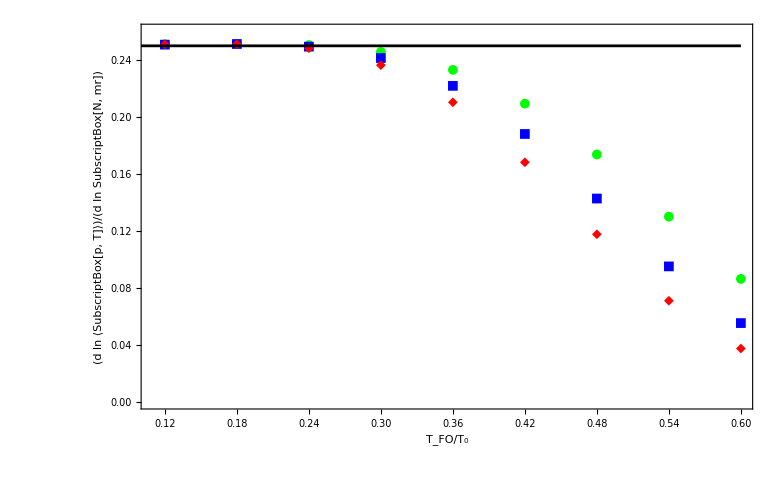

```mathematica
plt1=Table[{cs2vsslope[[k,j,1]]/T0Global,cs2vsslope[[k,j,2]]},{k,1,Length[cs2vsslope]},{j,1,Length[cs2vsslope[[k]]]}];
cs2=0.25;σtab={5.0, 7.5, 10};
legtab=Table[Style["σ="<>ToString[sig]<>" fm",22],{sig,σtab}];
Show[ListPlot[plt1,Frame->True,PlotRange->{0,cs2+0.01},FrameStyle->Directive[22,Black],PlotMarkers->{Automatic,Medium},PlotStyle->{Green,Blue,Red},PlotLegends->Placed[LineLegend[legtab],{0.15,0.25}]],Plot[cs2,{x,0,0.6},PlotStyle->Black,PlotLegends->Placed[LineLegend[{Style["c_s^2="<>ToString[cs2],22]}],{0.15,0.25}]],RotateLabel->{False,False}, FrameLabel->{Style["T_FO/T_0",24],Style["(d ln ⟨SubscriptBox[p, T]⟩)/(d ln SubscriptBox[N, mr])",24]}]
```

## Initial temperature profile display

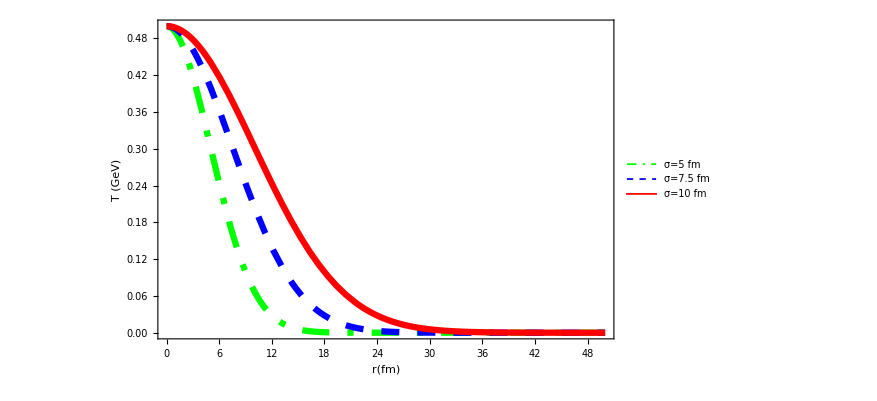

```mathematica
(*INITIAL TEMPERATURE PROFILE*)
sigtab={5,7.5,10};
Tcyl[r_,σ_,T0_]:=T0 E^(-r^2/(2 σ^2))
legtab=Table[Style["σ="<>ToString[s]<>" fm",27],{s,sigtab}];
pltT=Table[Tcyl[r,s,T0Global],{s,sigtab}];
Plot[pltT,{r,0,50},PlotRange->All,PlotLegends->Placed[LineLegend[legtab],{0.75,0.5}],Frame->True,FrameStyle->Directive[27,Black],FrameLabel->{Style["r(fm)",29],Style["T (GeV)",29]},PlotStyle->{{Thickness[0.007],Dashing[{0.03,0.02,0.007,0.02}],Green,CapForm["Round"]},{Thickness[0.007],Dashing[{0.02,0.02}],Blue,CapForm["Round"]},{Thickness[0.007],Red,CapForm["Round"]},{Thickness[0.007],Dashing[{0.007,0.02}],Darker[Green],CapForm["Round"]},{Thickness[0.007],Dashing[{0.03,0.02,0.007,0.02,0.007,0.02}],Purple,CapForm["Round"]}}]
```

## Various T_FO Hypersurfaces

```mathematica
tau0Global=.4;
T0Global=.5;
sigmaGlobal=5.;
NsampleHypersurface=100(*100*);

cs2=1/3;
tfotab={0.01,0.02,0.06};
cs2vsslope={};
resultslist={};
ct=1;

cs2Cte[T_]:=cs2;

hypersurfaceList=Table[With[{profile=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[{r},T0Global Exp[-r^2/2/sigmaGlobal^2]],Function[{r},0.00001],cs2Cte]},findHyperSurface[profile[[1]],profile[[2]],tfo,NsampleHypersurface]],{tfo,tfotab}];
(*--------------------------------------------------------------------------------------------------*)
```

```mathematica
pltleg1=Table[Style["T_FO/T_0="<>ToString[tfo/T0Global],22],{tfo,tfotab}];
ListPlot[hypersurfaceList[[;;,;;,{1,2}]],Joined->True,Frame->True,FrameStyle->Directive[22,Black],FrameLabel->{Style["τ(fm)",24],Style["r(fm)",24]},PlotStyle->{Black,{Red,Dashed},{Blue,Dotted}},PlotLegends->Placed[LineLegend[pltleg1],{0.25,0.75}]]
```

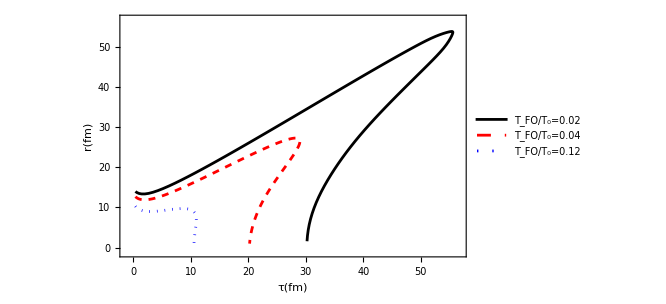

## Fixed T_FO value hypersurfaces for various cs2

```mathematica
tau0Global=.4;
T0Global=.5;
sigmaGlobal=5.;
NsampleHypersurface=100;

cs2tab={0.25,1/3};
tfo0=0.06;
hypersurfaceList2={};
ct=1;

Do[
cs2Cte[T_]:=cs2t;
With[{tfo=tfo0,profile=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[{r},T0Global Exp[-r^2/2/sigmaGlobal^2]],Function[{r},0.00001],cs2Cte]},AppendTo[hypersurfaceList2,findHyperSurface[profile[[1]],profile[[2]],tfo,NsampleHypersurface]]
]
,{cs2t,cs2tab}]

(*--------------------------------------------------------------------------------------------------*)
```

```mathematica
hypersurfaceList2
```

{{{0.4,13.9857,0.0195925,-0.0341807,0.00001},{0.419592,13.9516,0.0585021,-0.0930983,0.0110481},{0.478095,13.8585,0.0966798,-0.130351,0.0448154},{0.574774,13.7281,0.133856,-0.145294,0.102608},{0.70863,13.5828,0.169893,-0.143194,0.185069},{0.878523,13.4396,0.20468,-0.129375,0.291207},{1.0832,13.3103,0.238063,-0.107261,0.417936},{1.32127,13.203,0.269827,-0.0787817,0.560134},{1.59109,13.1242,0.299749,-0.0454145,0.711326},{1.89084,13.0788,0.327685,-0.00888733,0.864915},{2.21853,13.0699,0.353621,0.0288504,1.01544},{2.57215,13.0988,0.377653,0.0660647,1.15927},{2.9498,13.1648,0.399933,0.101552,1.29455},{3.34973,13.2664,0.42061,0.134663,1.42074},{3.77034,13.401,0.439814,0.165157,1.53807},{4.21016,13.5662,0.457642,0.193033,1.64716},{4.6678,13.7592,0.474167,0.218409,1.74875},{5.14197,13.9776,0.489445,0.241447,1.84359},{5.63141,14.2191,0.503517,0.262317,1.93238},{6.13493,14.4814,0.516438,0.281177,2.01573},{6.65137,14.7626,0.528201,0.298164,2.09419},{7.17957,15.0607,0.53882,0.313402,2.16819},{7.71839,15.3741,0.548327,0.326996,2.23814},{8.26671,15.7011,0.55674,0.339034,2.30437},{8.82345,16.0402,0.564075,0.349591,2.36715},{9.38753,16.3898,0.570363,0.358733,2.42675},{9.95789,16.7485,0.575632,0.366502,2.48337},{10.5335,17.115,0.579802,0.372948,2.5372},{11.1133,17.488,0.582932,0.378113,2.58839},{11.6963,17.8661,0.585035,0.382033,2.63707},{12.2813,18.2481,0.586121,0.384737,2.68337},{12.8674,18.6328,0.586289,0.386244,2.7274},{13.4537,19.0191,0.5854,0.386554,2.76924},{14.0391,19.4056,0.583462,0.385705,2.80898},{14.6226,19.7913,0.580522,0.383715,2.84668},{15.2031,20.1751,0.576593,0.380601,2.8824},{15.7797,20.5557,0.571748,0.376372,2.9162},{16.3514,20.932,0.566024,0.370998,2.94812},{16.9175,21.303,0.559138,0.364505,2.97821},{17.4766,21.6675,0.551258,0.356917,3.00649},{18.0278,22.0244,0.5424,0.348245,3.03299},{18.5702,22.3727,0.532582,0.338491,3.05774},{19.1028,22.7112,0.521956,0.32765,3.08076},{19.6248,23.0388,0.510435,0.315669,3.10207},{20.1352,23.3545,0.497683,0.302592,3.12165},{20.6329,23.6571,0.483951,0.288441,3.13951},{21.1169,23.9455,0.469259,0.27322,3.15568},{21.5861,24.2188,0.453623,0.256928,3.17013},{22.0397,24.4757,0.437057,0.239563,3.18288},{22.4768,24.7152,0.419569,0.221118,3.19391},{22.8964,24.9364,0.401549,0.201569,3.2032},{23.2979,25.1379,0.382291,0.180879,3.21072},{23.6802,25.3188,0.361903,0.159115,3.21643},{24.0421,25.4779,0.340592,0.136286,3.22033},{24.3827,25.6142,0.318375,0.112395,3.22238},{24.7011,25.7266,0.295271,0.0874481,3.22255},{24.9963,25.8141,0.271297,0.0614489,3.2208},{25.2676,25.8755,0.246471,0.0344044,3.21709},{25.5141,25.9099,0.220814,0.00632365,3.21135},{25.7349,25.9162,0.19435,-0.0227816,3.20353},{25.9293,25.8934,0.167105,-0.0528968,3.19357},{26.0964,25.8406,0.139112,-0.0840043,3.1814},{26.2355,25.7565,0.110409,-0.116082,3.16694},{26.3459,25.6405,0.0810396,-0.149106,3.15011},{26.4269,25.4914,0.0510564,-0.183045,3.13082},{26.478,25.3083,0.0205173,-0.217863,3.10897},{26.4985,25.0905,-0.0106426,-0.253484,3.08445},{26.4879,24.837,-0.0421573,-0.289738,3.0571},{26.4457,24.5472,-0.0738976,-0.326644,3.02684},{26.3718,24.2206,-0.105825,-0.364148,2.99354},{26.266,23.8564,-0.137795,-0.402183,2.95707},{26.1282,23.4543,-0.169635,-0.440673,2.9173},{25.9586,23.0136,-0.200545,-0.479402,2.87405},{25.758,22.5342,-0.231596,-0.518029,2.82702},{25.5264,22.0162,-0.262232,-0.556588,2.77614},{25.2642,21.4596,-0.291862,-0.594981,2.72127},{24.9723,20.8646,-0.318261,-0.632822,2.66225},{24.6541,20.2318,-0.345034,-0.669653,2.59867},{24.309,19.5621,-0.370158,-0.705484,2.53052},{23.9389,18.8566,-0.390049,-0.739982,2.45767},{23.5488,18.1166,-0.409323,-0.772463,2.37983},{23.1395,17.3442,-0.425583,-0.802822,2.29691},{22.7139,16.5414,-0.434794,-0.830726,2.20891},{22.2791,15.7106,-0.443245,-0.855487,2.11575},{21.8359,14.8551,-0.444355,-0.877015,2.01738},{21.3915,13.9781,-0.440929,-0.895144,1.91417},{20.9506,13.083,-0.432938,-0.909178,1.80613},{20.5177,12.1738,-0.417473,-0.920061,1.69368},{20.1002,11.2537,-0.398542,-0.927047,1.57743},{19.7016,10.3267,-0.3737,-0.931389,1.45753},{19.3279,9.39531,-0.344428,-0.933676,1.33506},{18.9835,8.46163,-0.313857,-0.934486,1.21009},{18.6697,7.52714,-0.27896,-0.935944,1.08322},{18.3907,6.5912,-0.244892,-0.938243,0.954697},{18.1458,5.65296,-0.210346,-0.942981,0.824222},{17.9355,4.70998,-0.176426,-0.950278,0.691647},{17.759,3.7597,-0.144489,-0.964349,0.556745},{17.6145,2.79535,-0.10731,-0.97357,0.418082},{17.5072,1.82178,-0.0638181,-0.986943,0.275817},{17.4434,0.834837,-0.0237418,-0.834837,0.128266}},{{0.4,13.9857,0.00540172,-0.0119911,0.00001},{0.405402,13.9738,0.0161777,-0.0350025,0.00303948},{0.421579,13.9388,0.0268747,-0.055344,0.0121996},{0.448454,13.8834,0.0374495,-0.0719259,0.0276841},{0.485904,13.8115,0.04787,-0.0843654,0.0497542},{0.533774,13.7271,0.0581149,-0.0928546,0.0786714},{0.591889,13.6343,0.0681714,-0.097926,0.114637},{0.66006,13.5363,0.0780321,-0.100235,0.157748},{0.738092,13.4361,0.0876924,-0.100412,0.207968},{0.825784,13.3357,0.0971476,-0.0989898,0.265114},{0.922932,13.2367,0.106391,-0.0963685,0.328845},{1.02932,13.1403,0.115413,-0.0928226,0.398665},{1.14474,13.0475,0.124198,-0.0885157,0.473925},{1.26893,12.959,0.132726,-0.0835288,0.553839},{1.40166,12.8755,0.140972,-0.0778953,0.637509},{1.54263,12.7976,0.148911,-0.0716341,0.723961},{1.69154,12.7259,0.156515,-0.0647795,0.812194},{1.84806,12.6612,0.163762,-0.0573993,0.90123},{2.01182,12.6038,0.170635,-0.0495994,0.990171},{2.18245,12.5542,0.177124,-0.0415152,1.07824},{2.35958,12.5126,0.183231,-0.0332966,1.16479},{2.54281,12.4793,0.188956,-0.0250917,1.24934},{2.73177,12.4543,0.194308,-0.0170331,1.33155},{2.92607,12.4372,0.199297,-0.00923204,1.4112},{3.12537,12.428,0.203934,-0.00177331,1.48816},{3.3293,12.4262,0.208232,0.00527992,1.5624},{3.53754,12.4315,0.2122,0.011888,1.63394},{3.74974,12.4434,0.215846,0.0180228,1.70282},{3.96558,12.4614,0.219177,0.023672,1.76912},{4.18476,12.4851,0.222204,0.02883,1.83293},{4.40696,12.5139,0.22493,0.0334979,1.89436},{4.63189,12.5474,0.227348,0.037681,1.95351},{4.85924,12.5851,0.229467,0.0413864,2.01045},{5.08871,12.6265,0.231289,0.0446229,2.0653},{5.32,12.6711,0.232814,0.0473988,2.11813},{5.55281,12.7185,0.234044,0.0497236,2.16901},{5.78686,12.7682,0.234979,0.0516053,2.21803},{6.02183,12.8198,0.235618,0.0530517,2.26524},{6.25745,12.8729,0.23596,0.05407,2.31071},{6.49341,12.9269,0.236006,0.0546663,2.35448},{6.72942,12.9816,0.235754,0.0548457,2.3966},{6.96517,13.0365,0.235204,0.0546126,2.43711},{7.20038,13.0911,0.234353,0.0539705,2.47605},{7.43473,13.145,0.2332,0.0529221,2.51343},{7.66793,13.198,0.231743,0.0514692,2.5493},{7.89967,13.2494,0.229982,0.0496129,2.58366},{8.12965,13.299,0.227912,0.0473534,2.61653},{8.35757,13.3464,0.225533,0.0446901,2.64793},{8.5831,13.3911,0.222842,0.0416219,2.67786},{8.80594,13.4327,0.219836,0.0381466,2.70633},{9.02578,13.4709,0.216512,0.0342621,2.73333},{9.24229,13.5051,0.212868,0.0299646,2.75886},{9.45516,13.5351,0.2089,0.0252502,2.78292},{9.66406,13.5603,0.204605,0.0201144,2.80549},{9.86866,13.5804,0.19998,0.0145517,2.82656},{10.0686,13.595,0.195021,0.00855605,2.84611},{10.2637,13.6036,0.189725,0.0021208,2.86412},{10.4534,13.6057,0.184087,-0.00476146,2.88056},{10.6375,13.6009,0.178104,-0.0120989,2.8954},{10.8156,13.5888,0.171772,-0.0199,2.90861},{10.9874,13.5689,0.165088,-0.0281746,2.92015},{11.1524,13.5407,0.158046,-0.0369329,2.92997},{11.3105,13.5038,0.150645,-0.0461855,2.93803},{11.4611,13.4576,0.142879,-0.0559443,2.94426},{11.604,13.4017,0.134746,-0.0662216,2.94861},{11.7388,13.3355,0.126243,-0.0770304,2.95101},{11.865,13.2584,0.117367,-0.0883845,2.95138},{11.9824,13.17,0.108117,-0.100298,2.94963},{12.0905,13.0697,0.0984901,-0.112787,2.94568},{12.189,12.957,0.0884859,-0.125865,2.93942},{12.2775,12.8311,0.0781048,-0.139551,2.93073},{12.3556,12.6915,0.0673469,-0.153859,2.9195},{12.4229,12.5377,0.0558247,-0.168806,2.90558},{12.4787,12.3689,0.0441946,-0.18441,2.88878},{12.5229,12.1845,0.0323405,-0.200691,2.86895},{12.5553,11.9838,0.0201635,-0.217668,2.84592},{12.5754,11.7661,0.00768473,-0.235357,2.81947},{12.5831,11.5308,-0.00507071,-0.253776,2.78937},{12.578,11.277,-0.0180732,-0.27294,2.75535},{12.56,11.004,-0.0312893,-0.292858,2.71713},{12.5287,10.7112,-0.0447262,-0.31354,2.67437},{12.484,10.3976,-0.0589686,-0.334952,2.6267},{12.425,10.0627,-0.0725287,-0.357098,2.57355},{12.3525,9.70559,-0.0859362,-0.380003,2.51461},{12.2665,9.32558,-0.0990596,-0.403654,2.44938},{12.1675,8.92193,-0.111749,-0.428019,2.3773},{12.0557,8.49391,-0.124086,-0.452983,2.2977},{11.9316,8.04093,-0.135541,-0.478305,2.20962},{11.7961,7.56262,-0.145639,-0.504046,2.11233},{11.6505,7.05858,-0.154074,-0.530112,2.00512},{11.4964,6.52847,-0.159913,-0.556237,1.88707},{11.3365,5.97223,-0.163119,-0.581746,1.7569},{11.1733,5.39048,-0.163628,-0.606568,1.61354},{11.0097,4.78391,-0.160017,-0.630415,1.45635},{10.8497,4.1535,-0.147963,-0.652143,1.28465},{10.7017,3.50136,-0.134198,-0.672773,1.0974},{10.5675,2.82858,-0.115531,-0.688722,0.895322},{10.452,2.13986,-0.0912921,-0.700629,0.680777},{10.3607,1.43923,-0.0595583,-0.693423,0.457294},{10.3012,0.74581,-0.0259403,-0.74581,0.234758}}}

```mathematica
pltleg1=Table[Style["c_s^2 ="<>ToString[cs2t],22],{cs2t,N[cs2tab,2]}];
ListPlot[hypersurfaceList2[[;;,;;,{1,2}]],Joined->True,Frame->True,FrameStyle->Directive[22,Black],FrameLabel->{Style["τ(fm)",24],Style["r(fm)",24]},PlotStyle->{Black,{Red,Dashed},{Blue,Dotted}},PlotLegends->Placed[LineLegend[pltleg1],{0.25,0.75}]]
```